# Graphing The Implied Volatility Smile

Khoa Tran - MATH 5111 - Professor Stojanovic - Assignment 3

In order to graph and observe the implied volatility smile, we use the data for option quotes of Google.
First, we import the data from the csv file and clean it in Mathematica:

```mathematica
SetDirectory["C:\\Users\\binbe\\Desktop\\lesson\\computational finance"];
fn=FileNames["2020-10-27*"][[1]];
DecimalTime[x_]:= x[[1]]+(FromDate[x]-FromDate[{x[[1]],1,1,0,0,0}])/(FromDate[{x[[1]]+1,1,1,0,0,0}]-FromDate[{x[[1]],1,1,0,0,0}])//N;
UnderlyingLegend ={"LAST","LX","Net Chng","BID","BX","ASK","AX","Size","Volume","Open","High","Low"};
AllOptionsData=Import[fn,"Data"];
timeOfRecord = With[{x=AllOptionsData[[1,1]]},DecimalTime[DateList[StringTake[x,{StringPosition[x," on"][[1,2]]+2,-1}]]]];
lbau = Position[UnderlyingLegend,#][[1,1]]&/@{"LAST","BID","ASK"};
OptionsLegend = {"","","LAST","LX","Net Chng","BID","BX","ASK","AX","Exp","Strike","BID","BX","ASK","AX","LAST","LX","Net Chng","",""};
lbacp=Transpose[Flatten/@(Position[OptionsLegend,#]&/@{"LAST","BID","ASK"})];
lbacp=Insert[lbacp,Flatten[Position[OptionsLegend,#]&/@{"Exp","Strike"}],2];
UnderlyingLBAPrices =AllOptionsData[[Position[AllOptionsData, {"LAST","LX","Net Chng","BID","BX","ASK","AX","Size","Volume","Open","High","Low"}][[1,1]]+1]][[#]]&/@lbau;
OptionsSeparators =Flatten[Position[AllOptionsData,{"","","LAST","LX","Net Chng","BID","BX","ASK","AX","Exp","Strike","BID","BX","ASK","AX","LAST","LX","Net Chng","",""}]];
OptionsSeparators2={1,-1}+#&/@Partition[OptionsSeparators,2,1];
recordLength=Length[{"","",0,"",0,629.6,"X",637.3,"X","4 DEC 20",960,0,"H",0.6,"Z",0.45,"N",0,"",""}];
AllOptionsData2 =Select[Take[AllOptionsData,#],Length[#]==recordLength&]&/@OptionsSeparators2;
AllRelevantOptionsData=Function[record,record[[#]]&/@#&/@lbacp]/@#&/@AllOptionsData2;
AllRelevantOptionsData2=Function[y,ReplacePart[y,{2,1}-> DecimalTime[DateList[y[[2,1]]]]]]/@#&/@AllRelevantOptionsData;
AllRelevantOptionsData3 = Function[y,ReplacePart[ReplacePart[y,1-> Mean[Drop[y[[1]],1]]],3-> Mean[Drop[y[[3]],1]]]]/@#&/@AllRelevantOptionsData2;
```

After cleaning the data, our data is stored in AllRelevantOptionsData3, which contains info on options as following:

```mathematica
AllRelevantOptionsData3[[1,1]]
```

{772.95,{2020.83,820},1.8}

with the first element is the mean of bid and ask prices for call option, the second element contains the maturity date and the strike price respectively, and the third element is the mean of bid and ask prices for the put option.
Next, we define the value functions for the call options, VC, and put options, VP, as following:

```mathematica
VC[t_,S_,T_,k_,a_,b_,σ_]:= 1/2 ⅇ^(b(t-T))(ⅇ^(a(t-T))S(Erf[(2Log[S/k]-(t-T)(σ^2+2a))/(2Sqrt[2] Sqrt[(T-t)σ^2])]+1)+k(Erfc[(2Log[S/k]-(t-T)(2a-σ^2))/(2Sqrt[2]Sqrt[(T-t)σ^2])]-2));
VP[t_,S_,T_,k_,a_,b_,σ_]:=1/2 ⅇ^(b(t-T))(k Erfc[(2Log[S/k]-(t-T)(2a-σ^2))/(2Sqrt[2]Sqrt[(T-t)σ^2])]-ⅇ^(a(t-T))S Erfc[(2Log[S/k]-(t-T)(σ^2+2a))/(2Sqrt[2]Sqrt[(T-t)σ^2])])
```

Then, we determine the implied volatility by solving for σ as VC[σ] = call price or VP[σ]= put price in the market data above. In order to graph the “smile”, we’ll calculate such implied volatility for all the strike price K at each maturity date. Note that here we loop through the strike prices and the maturity date by iterating through the column (col) and the row (row) of the data respectively (note, we iterate through each row first and then through columns of that row because the number of columns for each row might be different) , as following:

```mathematica
row = Length[AllRelevantOptionsData3];
put[r_,c_]:=FindRoot[AllRelevantOptionsData3[[r,c]][[3]]==VP[timeOfRecord,Mean[Drop[UnderlyingLBAPrices,1]],AllRelevantOptionsData3[[r,c]][[2,1]],AllRelevantOptionsData3[[r,c]][[2,2]], 0.0025-0.0001,0.0025,𝕡],{𝕡,Random [Real,{0,2}]}];
putvol =Table[𝕡/. put[r,c],{r,1,row},{c,1,Length[AllRelevantOptionsData3[[r]]]}];
call[r_,c_]:=FindRoot[AllRelevantOptionsData3[[r,c]][[1]]==VC[timeOfRecord,Mean[Drop[UnderlyingLBAPrices,1]],AllRelevantOptionsData3[[r,c]][[2,1]],AllRelevantOptionsData3[[r,c]][[2,2]], 0.0025-0.0001,0.0025,𝕡],{𝕡,Random [Real,{0,2}]}];
callvol =Table[𝕡/. call[r,c],{r,1,row},{c,1,Length[AllRelevantOptionsData3[[r]]]}];
```

6

Finally, we graph both of the put and call implied volatilities on 6 graphs (for 6 different maturity date in our data, according to 6 rows) to observe the smiles (red = put, blue = call):

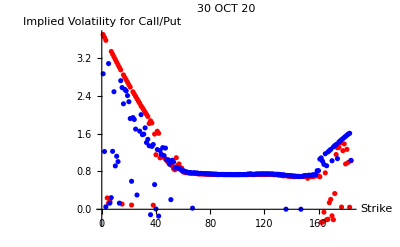
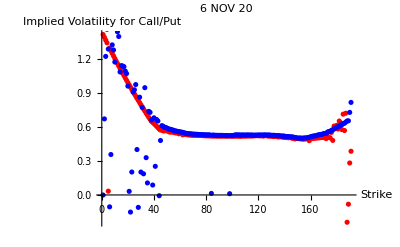
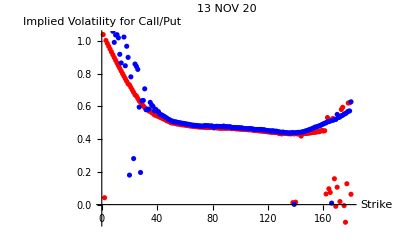
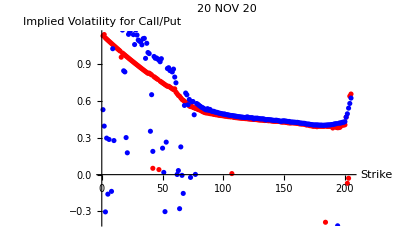
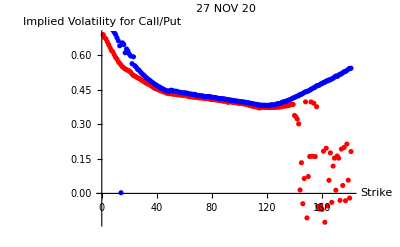
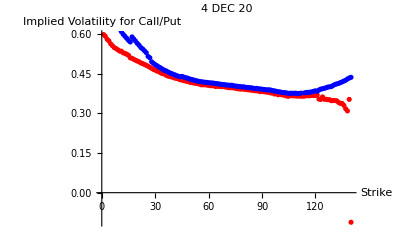

```mathematica
Show[Show[ListPlot[#[[1]],PlotStyle->Red,AxesLabel->{"Strike","Implied Volatility for Call/Put"},PlotRange -> All],ListPlot[#[[2]],PlotStyle->Blue],ImageSize->400],PlotLabel-> #[[3]]]&/@Transpose[{putvol,callvol,#[[1]]&/@(#[[2,1]]&/@#&/@AllRelevantOptionsData)}]
```

These smiles imply that volatilities in the market are not constant.